```mathematica
MyFolderX=NotebookDirectory[]
```

/Users/shawnliang/Desktop/Data & Code/Midterm/

```mathematica
(* Store filepath (string) of PersonData_ALL_N_354842_ALL.txt file in FilePathX *)
FilePathX=StringJoin[MyFolderX,"PersonData_ALL_N_354842_ALL.txt"]
```

/Users/shawnliang/Desktop/Data & Code/Midterm/PersonData_ALL_N_354842_ALL.txt

```mathematica
(* Import Data > Store in the local variabe "Din" *)
Din=Import[FilePathX,"CSV",CharacterEncoding-> "UTF8","TextDelimiters"->"\""];
```

```mathematica
NDataALL = Length[Din]
```

354842

```mathematica
1.Time Period Between 1920s and 1930s  --Woman Occupation Types in the United States [ During World War II ]
```

```mathematica
HeaderX={"Name","FullName","Gender","NationalityCountries","BirthDate","DeathDate","BirthPlace","DeathPlace","Occupation","Wives","Husbands"};

(* Choose from Dataset to obtain 1890s-1900s indivduals, and cleaning the data by getting rid of NotAvailable data, and rounding the year to decades.*)
```

```mathematica
DinFirst = Reap[For[i = 1, i<NDataALL, i++,
If[(ToExpression[StringDrop[Din[[i]][[5]],-7]]*10 == 1930 || (ToExpression[StringDrop[Din[[i]][[5]],-7]]*10 ==1940)) &&
(Din[[i]][[4]]== "UnitedStates")&&
(Din[[i]][[3]]== "Female")&&
(Din[[i]][[-3]]!= "NotAvailable"), Sow[Din[[i]]]
]]][[2]][[1]];
DinFirst[[1;;3]]
Length[DinFirst]
```

{{Abbe Lane,NotAvailable,Female,UnitedStates,1932-12-14,NotAvailable,NewYork;NewYork;UnitedStates,NotAvailable,actor;singer;dancer,NotAvailable,XavierCugat::63k36;Perry_Leff},{Abbey Lincoln,Anna Marie Wooldridge,Female,UnitedStates,1930-08-06,2010-08-14,Chicago;Illinois;UnitedStates,NewYork;NewYork;UnitedStates,singer/songwriter;actor,NotAvailable,MaxRoach::dxmg4},{Abby Dalton,Abby Dalton,Female,UnitedStates,1935-08-15,NotAvailable,LasVegas;Nevada;UnitedStates,NotAvailable,actor,NotAvailable,Jack_Smith;Joe_Mondragon}}

2670

```mathematica
2. Count Different Birth Years and Occupation Types from People Dataset
```

```mathematica
DBirthYearFirst = DinFirst
DBirthYearFirst= Reap[For[i = 1, i <= Length[DBirthYearFirst], i++,
Sow[ToExpression[StringDrop[DBirthYearFirst[[i]][[5]],-7]]*10]]][[2]][[1]];
```

{{Abbe Lane,NotAvailable,Female,UnitedStates,1932-12-14,NotAvailable,NewYork;NewYork;UnitedStates,NotAvailable,actor;singer;dancer,NotAvailable,XavierCugat::63k36;Perry_Leff},2668,{Verna Bloom,Verna Bloom,Female,UnitedStates,1938-08-07,2019-01-09,Lynn;Massachusetts;UnitedStates,BarHarbor;Maine;UnitedStates,actor,NotAvailable,JayCocks::g3p2n}}
 |  |  |  |

```mathematica
(*The Amount of in this dataset *)
Length[DBirthYearFirst]
DBirthYearFirst[[1;;10]]
```

2670

{1930,1930,1930,1940,1930,1940,1940,1930,1940,1940}

```mathematica
DOccupationsFirst= DinFirst
DOccupationsFirst= Reap[For[i = 1, i <= Length[DOccupationsFirst], i++,
Sow[DOccupationsFirst[[i]][[-3]]]]][[2]][[1]];
```

{{Abbe Lane,NotAvailable,Female,UnitedStates,1932-12-14,NotAvailable,NewYork;NewYork;UnitedStates,NotAvailable,actor;singer;dancer,NotAvailable,XavierCugat::63k36;Perry_Leff},2668,{Verna Bloom,Verna Bloom,Female,UnitedStates,1938-08-07,2019-01-09,Lynn;Massachusetts;UnitedStates,BarHarbor;Maine;UnitedStates,actor,NotAvailable,JayCocks::g3p2n}}
 |  |  |  |

```mathematica
(* Combine Year and Occupation data sets,
sepereate the occupations for when an indidual has more than one *)
```

```mathematica
DOC = Transpose[{DBirthYearFirst,DOccupationsFirst}];
DOC[[1;;2]]

SplitDOC = Reap[For[i = 1,i≤Length[DOC],i++,
s = StringSplit[DOC[[i,2]],";"];

For[j = 1,j≤ Length[s],j++,
Sow[{DOC[[i,1]],s[[j]]}]
]

]][[2]][[1]];
```

{{1930,actor;singer;dancer},{1930,singer/songwriter;actor}}

```mathematica
(* Tally the data and get the repeated times in dataset for years and occupations)
```

```mathematica
YDOC = Tally[Flatten[SplitDOC[[All,1]]]];
TableForm[YDOC]
```

1930 | 1150
1940 | 2473

```mathematica
3) Define Bipartite matrix associating people with their interests - use a sorted interest-index
```

```mathematica
(* Only take the first 200 data from the split data, because the larger the dataset, the messier the graphs.
This way we can have a more clear overall analysis.*)
NewDOC = SplitDOC[[1;;200]];
NewDOC[[-1]]
```

{1940,guitarist}

```mathematica
NewODOC = Tally[Flatten[NewDOC[[All,2]]]];
TableForm[NewODOC]
Length[NewODOC]
(* Below are the first 200 occupations and number of times they appear in 1890s - 1900s *)
```

actor | 39
singer | 10
dancer | 1
singer/songwriter | 1
social worker | 1
author | 15
judge | 8
businessperson | 7
politician | 18
musician | 4
activist | 5
playwright | 3
historian | 1
political activist | 2
anthropologist | 1
model | 4
novelist | 3
poet | 5
artist | 4
swimmer | 1
sports commentator | 1
academy award winner | 1
photographer | 2
painter | 2
famous by association | 2
television producer | 1
film director | 3
screenwriter | 1
journalist | 5
editor | 2
writer | 8
tv personality | 1
government | 2
radio talk show host | 1
academy award nominee | 1
fashion designer | 1
comedian | 1
athlete | 2
mathematician | 1
diplomat | 4
filmmaker | 2
attorney | 1
officer | 1
teacher | 2
guitarist | 2
composer | 1
drummer | 1
president | 1
investor | 1
poker player | 1
educator | 1
voice actor | 1
publisher | 1
farmer | 1
nurse | 1
professor | 2
literary critic | 1
translator | 1
singer-songwriter | 1
computer scientist | 1
songwriter | 1

61

```mathematica
(* Create "dictionary" which maps a person/interest name to an index *)
Clear[MapYeari]
For[i=1,i≤Length[YDOC],i++,MapYeari[YDOC[[i,1]]]=i; ];
```

```mathematica
MapYeari[YDOC[[1,1]]]
MapYeari[YDOC[[-1,1]]]
```

1

2

```mathematica
Clear[MapOccupationj];
For[i=1,i≤Length[NewODOC],i++,MapOccupationj[NewODOC[[i]][[1]]]=i; ];
```

```mathematica
Length[NewODOC]
```

61

```mathematica
(* Calculate the bipartite association matrix *)
YearOccupationMatrix=Array[0&,{Length[YDOC],Length[NewODOC]}];
For[i=1,i≤Length[NewDOC],i++,
nInt=MapOccupationj[NewDOC[[i,2]]];
mInt=MapYeari[NewDOC[[i,1]]];
YearOccupationMatrix[[mInt]][[nInt]]=YearOccupationMatrix[[mInt]][[nInt]]+1;
];

MatrixForm[YearOccupationMatrix]
```

(18 | 3 | 1 | 1 | 0 | 7 | 3 | 2 | 5 | 0 | 2 | 1 | 0 | 0 | 1 | 0 | 2 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 2 | 0 | 4 | 0 | 1 | 1 | 1 | 0 | 0 | 2 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 2 | 0 | 0 | 0 | 1 | 0
21 | 7 | 0 | 0 | 1 | 8 | 5 | 5 | 13 | 4 | 3 | 2 | 1 | 2 | 0 | 4 | 1 | 2 | 3 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 3 | 2 | 4 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 4 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1)

```mathematica
Show[Colorize[YearOccupationMatrix],ImageSize-> 400,AspectRatio-> 1]
```

-Graphics-

```mathematica
4) Define Year-Year and Occupation-Occupation association matrix using bipartite projection method
```

```mathematica
(* Year-Year association matrix *)
YearYearBipartiteProj=YearOccupationMatrix.Transpose[YearOccupationMatrix];
Length[YearYearBipartiteProj]
For[i=1,i≤ Length[YearYearBipartiteProj],i++, YearYearBipartiteProj[[i]][[i]]=0;] 
(* Delete diagonal elements *)
MatrixForm[YearYearBipartiteProj] (* Number of occupations are the same in these years*)
```

2

(0 | 591
591 | 0)

```mathematica
(* Occupation-Occupation association matrix *)
OccupationOccupationBipartiteProj=Transpose[YearOccupationMatrix].YearOccupationMatrix;
Length[OccupationOccupationBipartiteProj]
For[i=1,i≤ Length[OccupationOccupationBipartiteProj],i++, OccupationOccupationBipartiteProj[[i]][[i]]=0;] 
(* Delete diagonal elements *)

(* Display Matrix of first 20 occupaton to occupation *)
MatrixForm[OccupationOccupationBipartiteProj]
```

61

(0 | 201 | 18 | 18 | 21 | 294 | 159 | 141 | 363 | 84 | 99 | 60 | 21 | 42 | 18 | 84 | 57 | 96 | 81 | 21 | 21 | 21 | 42 | 42 | 39 | 21 | 60 | 21 | 99 | 42 | 156 | 21 | 39 | 18 | 18 | 21 | 21 | 36 | 21 | 84 | 39 | 21 | 21 | 36 | 42 | 21 | 21 | 18 | 21 | 21 | 21 | 21 | 18 | 18 | 21 | 36 | 21 | 21 | 21 | 18 | 21
201 | 0 | 3 | 3 | 7 | 77 | 44 | 41 | 106 | 28 | 27 | 17 | 7 | 14 | 3 | 28 | 13 | 23 | 24 | 7 | 7 | 7 | 14 | 14 | 10 | 7 | 17 | 7 | 27 | 14 | 40 | 7 | 10 | 3 | 3 | 7 | 7 | 6 | 7 | 28 | 10 | 7 | 7 | 6 | 14 | 7 | 7 | 3 | 7 | 7 | 7 | 7 | 3 | 3 | 7 | 6 | 7 | 7 | 7 | 3 | 7
18 | 3 | 0 | 1 | 0 | 7 | 3 | 2 | 5 | 0 | 2 | 1 | 0 | 0 | 1 | 0 | 2 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 2 | 0 | 4 | 0 | 1 | 1 | 1 | 0 | 0 | 2 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 2 | 0 | 0 | 0 | 1 | 0
18 | 3 | 1 | 0 | 0 | 7 | 3 | 2 | 5 | 0 | 2 | 1 | 0 | 0 | 1 | 0 | 2 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 2 | 0 | 4 | 0 | 1 | 1 | 1 | 0 | 0 | 2 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 2 | 0 | 0 | 0 | 1 | 0
21 | 7 | 0 | 0 | 0 | 8 | 5 | 5 | 13 | 4 | 3 | 2 | 1 | 2 | 0 | 4 | 1 | 2 | 3 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 3 | 2 | 4 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 4 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1
294 | 77 | 7 | 7 | 8 | 0 | 61 | 54 | 139 | 32 | 38 | 23 | 8 | 16 | 7 | 32 | 22 | 37 | 31 | 8 | 8 | 8 | 16 | 16 | 15 | 8 | 23 | 8 | 38 | 16 | 60 | 8 | 15 | 7 | 7 | 8 | 8 | 14 | 8 | 32 | 15 | 8 | 8 | 14 | 16 | 8 | 8 | 7 | 8 | 8 | 8 | 8 | 7 | 7 | 8 | 14 | 8 | 8 | 8 | 7 | 8
159 | 44 | 3 | 3 | 5 | 61 | 0 | 31 | 80 | 20 | 21 | 13 | 5 | 10 | 3 | 20 | 11 | 19 | 18 | 5 | 5 | 5 | 10 | 10 | 8 | 5 | 13 | 5 | 21 | 10 | 32 | 5 | 8 | 3 | 3 | 5 | 5 | 6 | 5 | 20 | 8 | 5 | 5 | 6 | 10 | 5 | 5 | 3 | 5 | 5 | 5 | 5 | 3 | 3 | 5 | 6 | 5 | 5 | 5 | 3 | 5
141 | 41 | 2 | 2 | 5 | 54 | 31 | 0 | 75 | 20 | 19 | 12 | 5 | 10 | 2 | 20 | 9 | 16 | 17 | 5 | 5 | 5 | 10 | 10 | 7 | 5 | 12 | 5 | 19 | 10 | 28 | 5 | 7 | 2 | 2 | 5 | 5 | 4 | 5 | 20 | 7 | 5 | 5 | 4 | 10 | 5 | 5 | 2 | 5 | 5 | 5 | 5 | 2 | 2 | 5 | 4 | 5 | 5 | 5 | 2 | 5
363 | 106 | 5 | 5 | 13 | 139 | 80 | 75 | 0 | 52 | 49 | 31 | 13 | 26 | 5 | 52 | 23 | 41 | 44 | 13 | 13 | 13 | 26 | 26 | 18 | 13 | 31 | 13 | 49 | 26 | 72 | 13 | 18 | 5 | 5 | 13 | 13 | 10 | 13 | 52 | 18 | 13 | 13 | 10 | 26 | 13 | 13 | 5 | 13 | 13 | 13 | 13 | 5 | 5 | 13 | 10 | 13 | 13 | 13 | 5 | 13
84 | 28 | 0 | 0 | 4 | 32 | 20 | 20 | 52 | 0 | 12 | 8 | 4 | 8 | 0 | 16 | 4 | 8 | 12 | 4 | 4 | 4 | 8 | 8 | 4 | 4 | 8 | 4 | 12 | 8 | 16 | 4 | 4 | 0 | 0 | 4 | 4 | 0 | 4 | 16 | 4 | 4 | 4 | 0 | 8 | 4 | 4 | 0 | 4 | 4 | 4 | 4 | 0 | 0 | 4 | 0 | 4 | 4 | 4 | 0 | 4
99 | 27 | 2 | 2 | 3 | 38 | 21 | 19 | 49 | 12 | 0 | 8 | 3 | 6 | 2 | 12 | 7 | 12 | 11 | 3 | 3 | 3 | 6 | 6 | 5 | 3 | 8 | 3 | 13 | 6 | 20 | 3 | 5 | 2 | 2 | 3 | 3 | 4 | 3 | 12 | 5 | 3 | 3 | 4 | 6 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 4 | 3 | 3 | 3 | 2 | 3
60 | 17 | 1 | 1 | 2 | 23 | 13 | 12 | 31 | 8 | 8 | 0 | 2 | 4 | 1 | 8 | 4 | 7 | 7 | 2 | 2 | 2 | 4 | 4 | 3 | 2 | 5 | 2 | 8 | 4 | 12 | 2 | 3 | 1 | 1 | 2 | 2 | 2 | 2 | 8 | 3 | 2 | 2 | 2 | 4 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2
21 | 7 | 0 | 0 | 1 | 8 | 5 | 5 | 13 | 4 | 3 | 2 | 0 | 2 | 0 | 4 | 1 | 2 | 3 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 3 | 2 | 4 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 4 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1
42 | 14 | 0 | 0 | 2 | 16 | 10 | 10 | 26 | 8 | 6 | 4 | 2 | 0 | 0 | 8 | 2 | 4 | 6 | 2 | 2 | 2 | 4 | 4 | 2 | 2 | 4 | 2 | 6 | 4 | 8 | 2 | 2 | 0 | 0 | 2 | 2 | 0 | 2 | 8 | 2 | 2 | 2 | 0 | 4 | 2 | 2 | 0 | 2 | 2 | 2 | 2 | 0 | 0 | 2 | 0 | 2 | 2 | 2 | 0 | 2
18 | 3 | 1 | 1 | 0 | 7 | 3 | 2 | 5 | 0 | 2 | 1 | 0 | 0 | 0 | 0 | 2 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 2 | 0 | 4 | 0 | 1 | 1 | 1 | 0 | 0 | 2 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 2 | 0 | 0 | 0 | 1 | 0
84 | 28 | 0 | 0 | 4 | 32 | 20 | 20 | 52 | 16 | 12 | 8 | 4 | 8 | 0 | 0 | 4 | 8 | 12 | 4 | 4 | 4 | 8 | 8 | 4 | 4 | 8 | 4 | 12 | 8 | 16 | 4 | 4 | 0 | 0 | 4 | 4 | 0 | 4 | 16 | 4 | 4 | 4 | 0 | 8 | 4 | 4 | 0 | 4 | 4 | 4 | 4 | 0 | 0 | 4 | 0 | 4 | 4 | 4 | 0 | 4
57 | 13 | 2 | 2 | 1 | 22 | 11 | 9 | 23 | 4 | 7 | 4 | 1 | 2 | 2 | 4 | 0 | 8 | 5 | 1 | 1 | 1 | 2 | 2 | 3 | 1 | 4 | 1 | 7 | 2 | 12 | 1 | 3 | 2 | 2 | 1 | 1 | 4 | 1 | 4 | 3 | 1 | 1 | 4 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 2 | 1 | 4 | 1 | 1 | 1 | 2 | 1
96 | 23 | 3 | 3 | 2 | 37 | 19 | 16 | 41 | 8 | 12 | 7 | 2 | 4 | 3 | 8 | 8 | 0 | 9 | 2 | 2 | 2 | 4 | 4 | 5 | 2 | 7 | 2 | 12 | 4 | 20 | 2 | 5 | 3 | 3 | 2 | 2 | 6 | 2 | 8 | 5 | 2 | 2 | 6 | 4 | 2 | 2 | 3 | 2 | 2 | 2 | 2 | 3 | 3 | 2 | 6 | 2 | 2 | 2 | 3 | 2
81 | 24 | 1 | 1 | 3 | 31 | 18 | 17 | 44 | 12 | 11 | 7 | 3 | 6 | 1 | 12 | 5 | 9 | 0 | 3 | 3 | 3 | 6 | 6 | 4 | 3 | 7 | 3 | 11 | 6 | 16 | 3 | 4 | 1 | 1 | 3 | 3 | 2 | 3 | 12 | 4 | 3 | 3 | 2 | 6 | 3 | 3 | 1 | 3 | 3 | 3 | 3 | 1 | 1 | 3 | 2 | 3 | 3 | 3 | 1 | 3
21 | 7 | 0 | 0 | 1 | 8 | 5 | 5 | 13 | 4 | 3 | 2 | 1 | 2 | 0 | 4 | 1 | 2 | 3 | 0 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 3 | 2 | 4 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 4 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1
21 | 7 | 0 | 0 | 1 | 8 | 5 | 5 | 13 | 4 | 3 | 2 | 1 | 2 | 0 | 4 | 1 | 2 | 3 | 1 | 0 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 3 | 2 | 4 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 4 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1
21 | 7 | 0 | 0 | 1 | 8 | 5 | 5 | 13 | 4 | 3 | 2 | 1 | 2 | 0 | 4 | 1 | 2 | 3 | 1 | 1 | 0 | 2 | 2 | 1 | 1 | 2 | 1 | 3 | 2 | 4 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 4 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1
42 | 14 | 0 | 0 | 2 | 16 | 10 | 10 | 26 | 8 | 6 | 4 | 2 | 4 | 0 | 8 | 2 | 4 | 6 | 2 | 2 | 2 | 0 | 4 | 2 | 2 | 4 | 2 | 6 | 4 | 8 | 2 | 2 | 0 | 0 | 2 | 2 | 0 | 2 | 8 | 2 | 2 | 2 | 0 | 4 | 2 | 2 | 0 | 2 | 2 | 2 | 2 | 0 | 0 | 2 | 0 | 2 | 2 | 2 | 0 | 2
42 | 14 | 0 | 0 | 2 | 16 | 10 | 10 | 26 | 8 | 6 | 4 | 2 | 4 | 0 | 8 | 2 | 4 | 6 | 2 | 2 | 2 | 4 | 0 | 2 | 2 | 4 | 2 | 6 | 4 | 8 | 2 | 2 | 0 | 0 | 2 | 2 | 0 | 2 | 8 | 2 | 2 | 2 | 0 | 4 | 2 | 2 | 0 | 2 | 2 | 2 | 2 | 0 | 0 | 2 | 0 | 2 | 2 | 2 | 0 | 2
39 | 10 | 1 | 1 | 1 | 15 | 8 | 7 | 18 | 4 | 5 | 3 | 1 | 2 | 1 | 4 | 3 | 5 | 4 | 1 | 1 | 1 | 2 | 2 | 0 | 1 | 3 | 1 | 5 | 2 | 8 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 4 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1
21 | 7 | 0 | 0 | 1 | 8 | 5 | 5 | 13 | 4 | 3 | 2 | 1 | 2 | 0 | 4 | 1 | 2 | 3 | 1 | 1 | 1 | 2 | 2 | 1 | 0 | 2 | 1 | 3 | 2 | 4 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 4 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1
60 | 17 | 1 | 1 | 2 | 23 | 13 | 12 | 31 | 8 | 8 | 5 | 2 | 4 | 1 | 8 | 4 | 7 | 7 | 2 | 2 | 2 | 4 | 4 | 3 | 2 | 0 | 2 | 8 | 4 | 12 | 2 | 3 | 1 | 1 | 2 | 2 | 2 | 2 | 8 | 3 | 2 | 2 | 2 | 4 | 2 | 2 | 1 | 2 | 2 | 2 | 2 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 1 | 2
21 | 7 | 0 | 0 | 1 | 8 | 5 | 5 | 13 | 4 | 3 | 2 | 1 | 2 | 0 | 4 | 1 | 2 | 3 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 0 | 3 | 2 | 4 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 4 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1
99 | 27 | 2 | 2 | 3 | 38 | 21 | 19 | 49 | 12 | 13 | 8 | 3 | 6 | 2 | 12 | 7 | 12 | 11 | 3 | 3 | 3 | 6 | 6 | 5 | 3 | 8 | 3 | 0 | 6 | 20 | 3 | 5 | 2 | 2 | 3 | 3 | 4 | 3 | 12 | 5 | 3 | 3 | 4 | 6 | 3 | 3 | 2 | 3 | 3 | 3 | 3 | 2 | 2 | 3 | 4 | 3 | 3 | 3 | 2 | 3
42 | 14 | 0 | 0 | 2 | 16 | 10 | 10 | 26 | 8 | 6 | 4 | 2 | 4 | 0 | 8 | 2 | 4 | 6 | 2 | 2 | 2 | 4 | 4 | 2 | 2 | 4 | 2 | 6 | 0 | 8 | 2 | 2 | 0 | 0 | 2 | 2 | 0 | 2 | 8 | 2 | 2 | 2 | 0 | 4 | 2 | 2 | 0 | 2 | 2 | 2 | 2 | 0 | 0 | 2 | 0 | 2 | 2 | 2 | 0 | 2
156 | 40 | 4 | 4 | 4 | 60 | 32 | 28 | 72 | 16 | 20 | 12 | 4 | 8 | 4 | 16 | 12 | 20 | 16 | 4 | 4 | 4 | 8 | 8 | 8 | 4 | 12 | 4 | 20 | 8 | 0 | 4 | 8 | 4 | 4 | 4 | 4 | 8 | 4 | 16 | 8 | 4 | 4 | 8 | 8 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 8 | 4 | 4 | 4 | 4 | 4
21 | 7 | 0 | 0 | 1 | 8 | 5 | 5 | 13 | 4 | 3 | 2 | 1 | 2 | 0 | 4 | 1 | 2 | 3 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 3 | 2 | 4 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 4 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1
39 | 10 | 1 | 1 | 1 | 15 | 8 | 7 | 18 | 4 | 5 | 3 | 1 | 2 | 1 | 4 | 3 | 5 | 4 | 1 | 1 | 1 | 2 | 2 | 2 | 1 | 3 | 1 | 5 | 2 | 8 | 1 | 0 | 1 | 1 | 1 | 1 | 2 | 1 | 4 | 2 | 1 | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1
18 | 3 | 1 | 1 | 0 | 7 | 3 | 2 | 5 | 0 | 2 | 1 | 0 | 0 | 1 | 0 | 2 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 2 | 0 | 4 | 0 | 1 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 2 | 0 | 0 | 0 | 1 | 0
18 | 3 | 1 | 1 | 0 | 7 | 3 | 2 | 5 | 0 | 2 | 1 | 0 | 0 | 1 | 0 | 2 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 2 | 0 | 4 | 0 | 1 | 1 | 0 | 0 | 0 | 2 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 2 | 0 | 0 | 0 | 1 | 0
21 | 7 | 0 | 0 | 1 | 8 | 5 | 5 | 13 | 4 | 3 | 2 | 1 | 2 | 0 | 4 | 1 | 2 | 3 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 3 | 2 | 4 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 4 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1
21 | 7 | 0 | 0 | 1 | 8 | 5 | 5 | 13 | 4 | 3 | 2 | 1 | 2 | 0 | 4 | 1 | 2 | 3 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 3 | 2 | 4 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 4 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1
36 | 6 | 2 | 2 | 0 | 14 | 6 | 4 | 10 | 0 | 4 | 2 | 0 | 0 | 2 | 0 | 4 | 6 | 2 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 4 | 0 | 8 | 0 | 2 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 4 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 4 | 0 | 0 | 0 | 2 | 0
21 | 7 | 0 | 0 | 1 | 8 | 5 | 5 | 13 | 4 | 3 | 2 | 1 | 2 | 0 | 4 | 1 | 2 | 3 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 3 | 2 | 4 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 4 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1
84 | 28 | 0 | 0 | 4 | 32 | 20 | 20 | 52 | 16 | 12 | 8 | 4 | 8 | 0 | 16 | 4 | 8 | 12 | 4 | 4 | 4 | 8 | 8 | 4 | 4 | 8 | 4 | 12 | 8 | 16 | 4 | 4 | 0 | 0 | 4 | 4 | 0 | 4 | 0 | 4 | 4 | 4 | 0 | 8 | 4 | 4 | 0 | 4 | 4 | 4 | 4 | 0 | 0 | 4 | 0 | 4 | 4 | 4 | 0 | 4
39 | 10 | 1 | 1 | 1 | 15 | 8 | 7 | 18 | 4 | 5 | 3 | 1 | 2 | 1 | 4 | 3 | 5 | 4 | 1 | 1 | 1 | 2 | 2 | 2 | 1 | 3 | 1 | 5 | 2 | 8 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 1 | 4 | 0 | 1 | 1 | 2 | 2 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1 | 1 | 1
21 | 7 | 0 | 0 | 1 | 8 | 5 | 5 | 13 | 4 | 3 | 2 | 1 | 2 | 0 | 4 | 1 | 2 | 3 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 3 | 2 | 4 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 4 | 1 | 0 | 1 | 0 | 2 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1
21 | 7 | 0 | 0 | 1 | 8 | 5 | 5 | 13 | 4 | 3 | 2 | 1 | 2 | 0 | 4 | 1 | 2 | 3 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 3 | 2 | 4 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 4 | 1 | 1 | 0 | 0 | 2 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1
36 | 6 | 2 | 2 | 0 | 14 | 6 | 4 | 10 | 0 | 4 | 2 | 0 | 0 | 2 | 0 | 4 | 6 | 2 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 4 | 0 | 8 | 0 | 2 | 2 | 2 | 0 | 0 | 4 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 4 | 0 | 0 | 0 | 2 | 0
42 | 14 | 0 | 0 | 2 | 16 | 10 | 10 | 26 | 8 | 6 | 4 | 2 | 4 | 0 | 8 | 2 | 4 | 6 | 2 | 2 | 2 | 4 | 4 | 2 | 2 | 4 | 2 | 6 | 4 | 8 | 2 | 2 | 0 | 0 | 2 | 2 | 0 | 2 | 8 | 2 | 2 | 2 | 0 | 0 | 2 | 2 | 0 | 2 | 2 | 2 | 2 | 0 | 0 | 2 | 0 | 2 | 2 | 2 | 0 | 2
21 | 7 | 0 | 0 | 1 | 8 | 5 | 5 | 13 | 4 | 3 | 2 | 1 | 2 | 0 | 4 | 1 | 2 | 3 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 3 | 2 | 4 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 4 | 1 | 1 | 1 | 0 | 2 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1
21 | 7 | 0 | 0 | 1 | 8 | 5 | 5 | 13 | 4 | 3 | 2 | 1 | 2 | 0 | 4 | 1 | 2 | 3 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 3 | 2 | 4 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 4 | 1 | 1 | 1 | 0 | 2 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1
18 | 3 | 1 | 1 | 0 | 7 | 3 | 2 | 5 | 0 | 2 | 1 | 0 | 0 | 1 | 0 | 2 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 2 | 0 | 4 | 0 | 1 | 1 | 1 | 0 | 0 | 2 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 2 | 0 | 0 | 0 | 1 | 0
21 | 7 | 0 | 0 | 1 | 8 | 5 | 5 | 13 | 4 | 3 | 2 | 1 | 2 | 0 | 4 | 1 | 2 | 3 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 3 | 2 | 4 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 4 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1
21 | 7 | 0 | 0 | 1 | 8 | 5 | 5 | 13 | 4 | 3 | 2 | 1 | 2 | 0 | 4 | 1 | 2 | 3 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 3 | 2 | 4 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 4 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1
21 | 7 | 0 | 0 | 1 | 8 | 5 | 5 | 13 | 4 | 3 | 2 | 1 | 2 | 0 | 4 | 1 | 2 | 3 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 3 | 2 | 4 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 4 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1
21 | 7 | 0 | 0 | 1 | 8 | 5 | 5 | 13 | 4 | 3 | 2 | 1 | 2 | 0 | 4 | 1 | 2 | 3 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 3 | 2 | 4 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 4 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1
18 | 3 | 1 | 1 | 0 | 7 | 3 | 2 | 5 | 0 | 2 | 1 | 0 | 0 | 1 | 0 | 2 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 2 | 0 | 4 | 0 | 1 | 1 | 1 | 0 | 0 | 2 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | 0 | 0 | 0 | 1 | 0
18 | 3 | 1 | 1 | 0 | 7 | 3 | 2 | 5 | 0 | 2 | 1 | 0 | 0 | 1 | 0 | 2 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 2 | 0 | 4 | 0 | 1 | 1 | 1 | 0 | 0 | 2 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0
21 | 7 | 0 | 0 | 1 | 8 | 5 | 5 | 13 | 4 | 3 | 2 | 1 | 2 | 0 | 4 | 1 | 2 | 3 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 3 | 2 | 4 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 4 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1
36 | 6 | 2 | 2 | 0 | 14 | 6 | 4 | 10 | 0 | 4 | 2 | 0 | 0 | 2 | 0 | 4 | 6 | 2 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 4 | 0 | 8 | 0 | 2 | 2 | 2 | 0 | 0 | 4 | 0 | 0 | 2 | 0 | 0 | 4 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 2 | 0
21 | 7 | 0 | 0 | 1 | 8 | 5 | 5 | 13 | 4 | 3 | 2 | 1 | 2 | 0 | 4 | 1 | 2 | 3 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 3 | 2 | 4 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 4 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1
21 | 7 | 0 | 0 | 1 | 8 | 5 | 5 | 13 | 4 | 3 | 2 | 1 | 2 | 0 | 4 | 1 | 2 | 3 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 3 | 2 | 4 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 4 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1
21 | 7 | 0 | 0 | 1 | 8 | 5 | 5 | 13 | 4 | 3 | 2 | 1 | 2 | 0 | 4 | 1 | 2 | 3 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 3 | 2 | 4 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 4 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1
18 | 3 | 1 | 1 | 0 | 7 | 3 | 2 | 5 | 0 | 2 | 1 | 0 | 0 | 1 | 0 | 2 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 2 | 0 | 4 | 0 | 1 | 1 | 1 | 0 | 0 | 2 | 0 | 0 | 1 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 2 | 0 | 0 | 0 | 0 | 0
21 | 7 | 0 | 0 | 1 | 8 | 5 | 5 | 13 | 4 | 3 | 2 | 1 | 2 | 0 | 4 | 1 | 2 | 3 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 3 | 2 | 4 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 4 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 0)

```mathematica
(* Degree Distribution *)
DegreeX=Total[Sign[#]]&/@OccupationOccupationBipartiteProj
```

{60,60,28,28,48,60,60,60,60,48,60,60,48,48,28,48,60,60,60,48,48,48,48,48,60,48,60,48,60,48,60,48,60,28,28,48,48,28,48,48,60,48,48,28,48,48,48,28,48,48,48,48,28,28,48,28,48,48,48,28,48}

```mathematica
5) WeightedAdjacencyGraph[ ]
```

```mathematica
mat=Replace[OccupationOccupationBipartiteProj,0->Infinity,{2}]; (*  0s represented by infinity in WeightedAdjacencyGraph[ ] *)
OName=NewODOC[[All,1]];

(* Set Labels : The "keys" for each node will be the name stored in OName *)
NameFontSizeX=20;
NodeColorX=Black;
LabelsetBlack=Table[OName[[i]]->Placed[ Style[OName[[i]],FontFamily->"Helvetica",NameFontSizeX,NodeColorX],Center],{i,Length[OName]}]
```

{actor→Placed[actor,Center],singer→Placed[singer,Center],dancer→Placed[dancer,Center],singer/songwriter→Placed[singer/songwriter,Center],social worker→Placed[social worker,Center],author→Placed[author,Center],judge→Placed[judge,Center],businessperson→Placed[businessperson,Center],politician→Placed[politician,Center],musician→Placed[musician,Center],activist→Placed[activist,Center],playwright→Placed[playwright,Center],historian→Placed[historian,Center],political activist→Placed[political activist,Center],anthropologist→Placed[anthropologist,Center],model→Placed[model,Center],novelist→Placed[novelist,Center],poet→Placed[poet,Center],artist→Placed[artist,Center],swimmer→Placed[swimmer,Center],sports commentator→Placed[sports commentator,Center],academy award winner→Placed[academy award winner,Center],photographer→Placed[photographer,Center],painter→Placed[painter,Center],famous by association→Placed[famous by association,Center],television producer→Placed[television producer,Center],film director→Placed[film director,Center],screenwriter→Placed[screenwriter,Center],journalist→Placed[journalist,Center],editor→Placed[editor,Center],writer→Placed[writer,Center],tv personality→Placed[tv personality,Center],government→Placed[government,Center],radio talk show host→Placed[radio talk show host,Center],academy award nominee→Placed[academy award nominee,Center],fashion designer→Placed[fashion designer,Center],comedian→Placed[comedian,Center],athlete→Placed[athlete,Center],mathematician→Placed[mathematician,Center],diplomat→Placed[diplomat,Center],filmmaker→Placed[filmmaker,Center],attorney→Placed[attorney,Center],officer→Placed[officer,Center],teacher→Placed[teacher,Center],guitarist→Placed[guitarist,Center],composer→Placed[composer,Center],drummer→Placed[drummer,Center],president→Placed[president,Center],investor→Placed[investor,Center],poker player→Placed[poker player,Center],educator→Placed[educator,Center],voice actor→Placed[voice actor,Center],publisher→Placed[publisher,Center],farmer→Placed[farmer,Center],nurse→Placed[nurse,Center],professor→Placed[professor,Center],literary critic→Placed[literary critic,Center],translator→Placed[translator,Center],singer-songwriter→Placed[singer-songwriter,Center],computer scientist→Placed[computer scientist,Center],songwriter→Placed[songwriter,Center]}

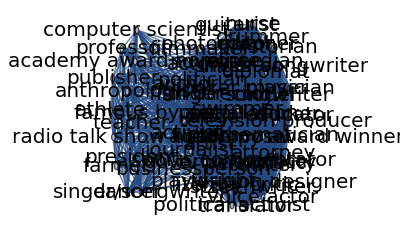

```mathematica
(* Plot Network - an ugly mess *)
g=WeightedAdjacencyGraph[OName,mat,VertexLabels->LabelsetBlack]
```

```mathematica
Clustering Coefficients - to what degree are neighbors connected?
```

```mathematica
(* Global - Network-level characteristic: What fraction of possible triangles (1st order cycle) exist in the network *)
N[GlobalClusteringCoefficient[g]]
```

0.907695

```mathematica
(* Local - Node-level characteristic: What fraction of possible triangles (1st order cycle) exist in the network *)LClusteringCoeffX=N[LocalClusteringCoefficient[g]]
Mean[LClusteringCoeffX]
N[MeanClusteringCoefficient[g]] (* Gives same result as above *)
```

{0.783051,0.783051,1.,1.,1.,0.783051,0.783051,0.783051,0.783051,1.,0.783051,0.783051,1.,1.,1.,1.,0.783051,0.783051,0.783051,1.,1.,1.,1.,1.,0.783051,1.,0.783051,1.,0.783051,1.,0.783051,1.,0.783051,1.,1.,1.,1.,1.,1.,1.,0.783051,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

0.939539

0.939539

```mathematica
Length[LClusteringCoeffX]
```

61

```mathematica
Length[OName]
```

61

```mathematica
Sort[Thread[Rule[OName,LClusteringCoeffX]],#1[[2]]>#2[[2]]&]
```

{songwriter→1.,computer scientist→1.,singer-songwriter→1.,translator→1.,literary critic→1.,professor→1.,nurse→1.,farmer→1.,publisher→1.,voice actor→1.,educator→1.,poker player→1.,investor→1.,president→1.,drummer→1.,composer→1.,guitarist→1.,teacher→1.,officer→1.,attorney→1.,diplomat→1.,mathematician→1.,athlete→1.,comedian→1.,fashion designer→1.,academy award nominee→1.,radio talk show host→1.,tv personality→1.,editor→1.,screenwriter→1.,television producer→1.,painter→1.,photographer→1.,academy award winner→1.,sports commentator→1.,swimmer→1.,model→1.,anthropologist→1.,political activist→1.,historian→1.,musician→1.,social worker→1.,singer/songwriter→1.,dancer→1.,filmmaker→0.783051,government→0.783051,writer→0.783051,journalist→0.783051,film director→0.783051,famous by association→0.783051,artist→0.783051,poet→0.783051,novelist→0.783051,playwright→0.783051,activist→0.783051,politician→0.783051,businessperson→0.783051,judge→0.783051,author→0.783051,singer→0.783051,actor→0.783051}

{{60,0.783051},{60,0.783051},{28,1.},{28,1.},{48,1.},{60,0.783051},{60,0.783051},{60,0.783051},{60,0.783051},{48,1.},{60,0.783051},{60,0.783051},{48,1.},{48,1.},{28,1.},{48,1.},{60,0.783051},{60,0.783051},{60,0.783051},{48,1.},{48,1.},{48,1.},{48,1.},{48,1.},{60,0.783051},{48,1.},{60,0.783051},{48,1.},{60,0.783051},{48,1.},{60,0.783051},{48,1.},{60,0.783051},{28,1.},{28,1.},{48,1.},{48,1.},{28,1.},{48,1.},{48,1.},{60,0.783051},{48,1.},{48,1.},{28,1.},{48,1.},{48,1.},{48,1.},{28,1.},{48,1.},{48,1.},{48,1.},{48,1.},{28,1.},{28,1.},{48,1.},{28,1.},{48,1.},{48,1.},{48,1.},{28,1.},{48,1.}}

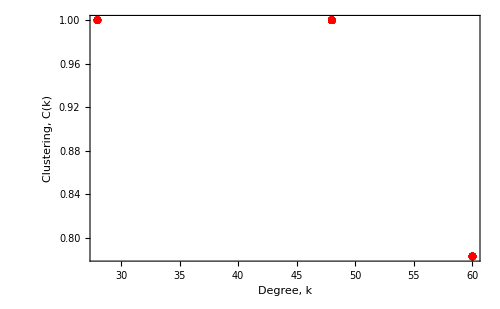

```mathematica
DegreeClusteringX=Thread[{DegreeX,LClusteringCoeffX}]

ListPlot[DegreeClusteringX,
PlotRange-> All,
PlotStyle->Directive[Red,10],
LabelStyle -> Directive[Black,FontSize->20,FontFamily-> "Helvetica"],
Frame->True,
ImageSize->{500,Automatic},
FrameLabel->{"Degree, k","Clustering, C(k)"},
ImageSize->500]
```

```mathematica
Improve network visualization layout
```

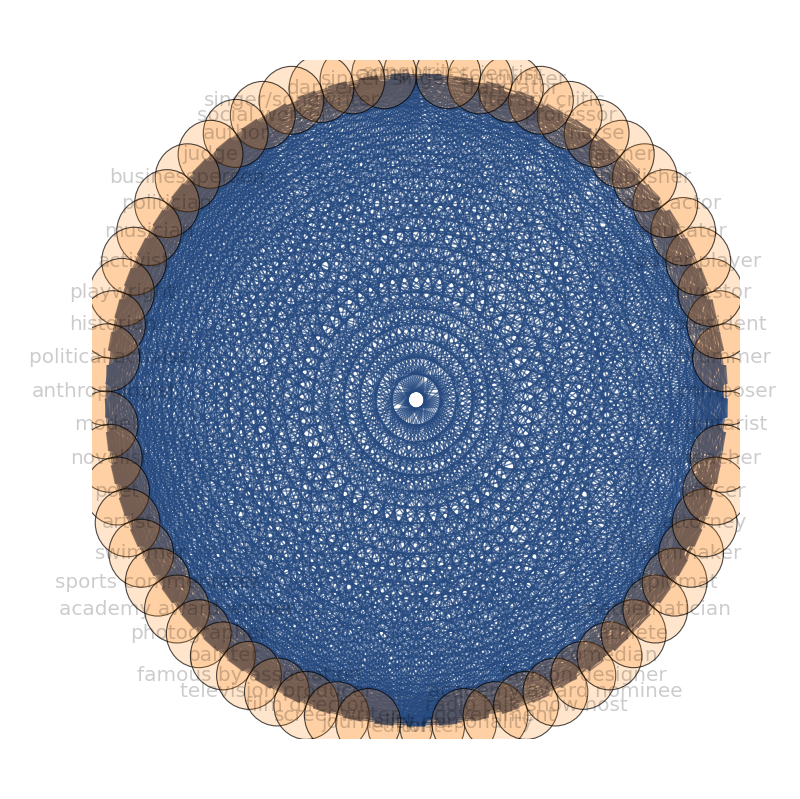

```mathematica
Circlesize=0.05;
r=Array[Circlesize&,Length[OName]]; (* Circle radius list *)

g=WeightedAdjacencyGraph[OName,mat,VertexLabels->LabelsetBlack,VertexSize->Scaled[.10],VertexStyle->Directive[Orange,Opacity[.2]],GraphLayout->{"CircularEmbedding"} ,ImageSize->800]
```

```mathematica
6) Modify the link color and thickness
```

```mathematica
(* AbsoluteOptions[ ]: gives the absolute settings of options specified in an expression such as a graphics object. *)
gEdWe=AbsoluteOptions[g,EdgeWeight][[All,2]][[1]]  (* Get list of edge weights associated with each edge *)
Max[gEdWe]
```

{201,18,18,21,294,159,141,363,84,99,60,21,42,18,84,57,96,81,21,21,21,42,42,39,21,60,21,99,42,156,21,39,18,18,21,21,36,21,84,39,21,21,36,42,21,21,18,21,21,21,21,18,18,21,36,21,21,21,18,21,3,3,7,77,44,41,106,28,27,17,7,14,3,28,13,23,24,7,7,7,14,14,10,7,17,7,27,14,40,7,10,3,3,7,7,6,7,28,10,7,7,6,14,7,7,3,7,7,7,7,3,3,7,6,7,7,7,3,7,1,7,3,2,5,2,1,1,2,3,1,1,1,2,4,1,1,1,2,1,2,1,1,1,2,1,7,3,2,5,2,1,1,2,3,1,1,1,2,4,1,1,1,2,1,2,1,1,1,2,1,8,5,5,13,4,3,2,1,2,4,1,2,3,1,1,1,2,2,1,1,2,1,3,2,4,1,1,1,1,1,4,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,61,54,139,32,38,23,8,16,7,32,22,37,31,8,8,8,16,16,15,8,23,8,38,16,60,8,15,7,7,8,8,14,8,32,15,8,8,14,16,8,8,7,8,8,8,8,7,7,8,14,8,8,8,7,8,31,80,20,21,13,5,10,3,20,11,19,18,5,5,5,10,10,8,5,13,5,21,10,32,5,8,3,3,5,5,6,5,20,8,5,5,6,10,5,5,3,5,5,5,5,3,3,5,6,5,5,5,3,5,75,20,19,12,5,10,2,20,9,16,17,5,5,5,10,10,7,5,12,5,19,10,28,5,7,2,2,5,5,4,5,20,7,5,5,4,10,5,5,2,5,5,5,5,2,2,5,4,5,5,5,2,5,52,49,31,13,26,5,52,23,41,44,13,13,13,26,26,18,13,31,13,49,26,72,13,18,5,5,13,13,10,13,52,18,13,13,10,26,13,13,5,13,13,13,13,5,5,13,10,13,13,13,5,13,12,8,4,8,16,4,8,12,4,4,4,8,8,4,4,8,4,12,8,16,4,4,4,4,4,16,4,4,4,8,4,4,4,4,4,4,4,4,4,4,4,8,3,6,2,12,7,12,11,3,3,3,6,6,5,3,8,3,13,6,20,3,5,2,2,3,3,4,3,12,5,3,3,4,6,3,3,2,3,3,3,3,2,2,3,4,3,3,3,2,3,2,4,1,8,4,7,7,2,2,2,4,4,3,2,5,2,8,4,12,2,3,1,1,2,2,2,2,8,3,2,2,2,4,2,2,1,2,2,2,2,1,1,2,2,2,2,2,1,2,2,4,1,2,3,1,1,1,2,2,1,1,2,1,3,2,4,1,1,1,1,1,4,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,8,2,4,6,2,2,2,4,4,2,2,4,2,6,4,8,2,2,2,2,2,8,2,2,2,4,2,2,2,2,2,2,2,2,2,2,2,2,3,1,1,1,2,4,1,1,1,2,1,2,1,1,1,2,1,4,8,12,4,4,4,8,8,4,4,8,4,12,8,16,4,4,4,4,4,16,4,4,4,8,4,4,4,4,4,4,4,4,4,4,4,8,5,1,1,1,2,2,3,1,4,1,7,2,12,1,3,2,2,1,1,4,1,4,3,1,1,4,2,1,1,2,1,1,1,1,2,2,1,4,1,1,1,2,1,9,2,2,2,4,4,5,2,7,2,12,4,20,2,5,3,3,2,2,6,2,8,5,2,2,6,4,2,2,3,2,2,2,2,3,3,2,6,2,2,2,3,2,3,3,3,6,6,4,3,7,3,11,6,16,3,4,1,1,3,3,2,3,12,4,3,3,2,6,3,3,1,3,3,3,3,1,1,3,2,3,3,3,1,3,1,1,2,2,1,1,2,1,3,2,4,1,1,1,1,1,4,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,2,1,3,2,4,1,1,1,1,1,4,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,2,1,3,2,4,1,1,1,1,1,4,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,4,2,2,4,2,6,4,8,2,2,2,2,2,8,2,2,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,4,2,6,4,8,2,2,2,2,2,8,2,2,2,4,2,2,2,2,2,2,2,2,2,2,2,1,3,1,5,2,8,1,2,1,1,1,1,2,1,4,2,1,1,2,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,1,3,2,4,1,1,1,1,1,4,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,8,4,12,2,3,1,1,2,2,2,2,8,3,2,2,2,4,2,2,1,2,2,2,2,1,1,2,2,2,2,2,1,2,3,2,4,1,1,1,1,1,4,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,6,20,3,5,2,2,3,3,4,3,12,5,3,3,4,6,3,3,2,3,3,3,3,2,2,3,4,3,3,3,2,3,8,2,2,2,2,2,8,2,2,2,4,2,2,2,2,2,2,2,2,2,2,2,4,8,4,4,4,4,8,4,16,8,4,4,8,8,4,4,4,4,4,4,4,4,4,4,8,4,4,4,4,4,1,1,1,1,4,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,4,2,1,1,2,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,2,1,1,1,2,1,2,1,2,1,1,1,2,1,1,1,4,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,4,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,4,2,2,2,4,2,4,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,4,4,4,8,4,4,4,4,4,4,4,4,4,4,4,1,1,2,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,2,2,4,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,2,1,1,1,1,1,1}

363

```mathematica
(* Use linear transform to rescale edge weight values to be from 0 to 1 *)
gEdWe=Rescale[gEdWe,{0,Max[gEdWe]},{0,1}]
```

{67/121,6/121,6/121,7/121,98/121,53/121,47/121,1,28/121,3/11,20/121,7/121,14/121,6/121,28/121,19/121,32/121,27/121,7/121,7/121,7/121,14/121,14/121,13/121,7/121,20/121,7/121,3/11,14/121,52/121,7/121,13/121,6/121,6/121,7/121,7/121,12/121,7/121,28/121,13/121,7/121,7/121,12/121,14/121,7/121,7/121,6/121,7/121,7/121,7/121,7/121,6/121,6/121,7/121,12/121,7/121,7/121,7/121,6/121,7/121,1/121,1/121,7/363,7/33,4/33,41/363,106/363,28/363,9/121,17/363,7/363,14/363,1/121,28/363,13/363,23/363,8/121,7/363,7/363,7/363,14/363,14/363,10/363,7/363,17/363,7/363,9/121,14/363,40/363,7/363,10/363,1/121,1/121,7/363,7/363,2/121,7/363,28/363,10/363,7/363,7/363,2/121,14/363,7/363,7/363,1/121,7/363,7/363,7/363,7/363,1/121,1/121,7/363,2/121,7/363,7/363,7/363,1/121,7/363,1/363,7/363,1/121,2/363,5/363,2/363,1/363,1/363,2/363,1/121,1/363,1/363,1/363,2/363,4/363,1/363,1/363,1/363,2/363,1/363,2/363,1/363,1/363,1/363,2/363,1/363,7/363,1/121,2/363,5/363,2/363,1/363,1/363,2/363,1/121,1/363,1/363,1/363,2/363,4/363,1/363,1/363,1/363,2/363,1/363,2/363,1/363,1/363,1/363,2/363,1/363,8/363,5/363,5/363,13/363,4/363,1/121,2/363,1/363,2/363,4/363,1/363,2/363,1/121,1/363,1/363,1/363,2/363,2/363,1/363,1/363,2/363,1/363,1/121,2/363,4/363,1/363,1/363,1/363,1/363,1/363,4/363,1/363,1/363,1/363,2/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,61/363,18/121,139/363,32/363,38/363,23/363,8/363,16/363,7/363,32/363,2/33,37/363,31/363,8/363,8/363,8/363,16/363,16/363,5/121,8/363,23/363,8/363,38/363,16/363,20/121,8/363,5/121,7/363,7/363,8/363,8/363,14/363,8/363,32/363,5/121,8/363,8/363,14/363,16/363,8/363,8/363,7/363,8/363,8/363,8/363,8/363,7/363,7/363,8/363,14/363,8/363,8/363,8/363,7/363,8/363,31/363,80/363,20/363,7/121,13/363,5/363,10/363,1/121,20/363,1/33,19/363,6/121,5/363,5/363,5/363,10/363,10/363,8/363,5/363,13/363,5/363,7/121,10/363,32/363,5/363,8/363,1/121,1/121,5/363,5/363,2/121,5/363,20/363,8/363,5/363,5/363,2/121,10/363,5/363,5/363,1/121,5/363,5/363,5/363,5/363,1/121,1/121,5/363,2/121,5/363,5/363,5/363,1/121,5/363,25/121,20/363,19/363,4/121,5/363,10/363,2/363,20/363,3/121,16/363,17/363,5/363,5/363,5/363,10/363,10/363,7/363,5/363,4/121,5/363,19/363,10/363,28/363,5/363,7/363,2/363,2/363,5/363,5/363,4/363,5/363,20/363,7/363,5/363,5/363,4/363,10/363,5/363,5/363,2/363,5/363,5/363,5/363,5/363,2/363,2/363,5/363,4/363,5/363,5/363,5/363,2/363,5/363,52/363,49/363,31/363,13/363,26/363,5/363,52/363,23/363,41/363,4/33,13/363,13/363,13/363,26/363,26/363,6/121,13/363,31/363,13/363,49/363,26/363,24/121,13/363,6/121,5/363,5/363,13/363,13/363,10/363,13/363,52/363,6/121,13/363,13/363,10/363,26/363,13/363,13/363,5/363,13/363,13/363,13/363,13/363,5/363,5/363,13/363,10/363,13/363,13/363,13/363,5/363,13/363,4/121,8/363,4/363,8/363,16/363,4/363,8/363,4/121,4/363,4/363,4/363,8/363,8/363,4/363,4/363,8/363,4/363,4/121,8/363,16/363,4/363,4/363,4/363,4/363,4/363,16/363,4/363,4/363,4/363,8/363,4/363,4/363,4/363,4/363,4/363,4/363,4/363,4/363,4/363,4/363,4/363,8/363,1/121,2/121,2/363,4/121,7/363,4/121,1/33,1/121,1/121,1/121,2/121,2/121,5/363,1/121,8/363,1/121,13/363,2/121,20/363,1/121,5/363,2/363,2/363,1/121,1/121,4/363,1/121,4/121,5/363,1/121,1/121,4/363,2/121,1/121,1/121,2/363,1/121,1/121,1/121,1/121,2/363,2/363,1/121,4/363,1/121,1/121,1/121,2/363,1/121,2/363,4/363,1/363,8/363,4/363,7/363,7/363,2/363,2/363,2/363,4/363,4/363,1/121,2/363,5/363,2/363,8/363,4/363,4/121,2/363,1/121,1/363,1/363,2/363,2/363,2/363,2/363,8/363,1/121,2/363,2/363,2/363,4/363,2/363,2/363,1/363,2/363,2/363,2/363,2/363,1/363,1/363,2/363,2/363,2/363,2/363,2/363,1/363,2/363,2/363,4/363,1/363,2/363,1/121,1/363,1/363,1/363,2/363,2/363,1/363,1/363,2/363,1/363,1/121,2/363,4/363,1/363,1/363,1/363,1/363,1/363,4/363,1/363,1/363,1/363,2/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,8/363,2/363,4/363,2/121,2/363,2/363,2/363,4/363,4/363,2/363,2/363,4/363,2/363,2/121,4/363,8/363,2/363,2/363,2/363,2/363,2/363,8/363,2/363,2/363,2/363,4/363,2/363,2/363,2/363,2/363,2/363,2/363,2/363,2/363,2/363,2/363,2/363,2/363,1/121,1/363,1/363,1/363,2/363,4/363,1/363,1/363,1/363,2/363,1/363,2/363,1/363,1/363,1/363,2/363,1/363,4/363,8/363,4/121,4/363,4/363,4/363,8/363,8/363,4/363,4/363,8/363,4/363,4/121,8/363,16/363,4/363,4/363,4/363,4/363,4/363,16/363,4/363,4/363,4/363,8/363,4/363,4/363,4/363,4/363,4/363,4/363,4/363,4/363,4/363,4/363,4/363,8/363,5/363,1/363,1/363,1/363,2/363,2/363,1/121,1/363,4/363,1/363,7/363,2/363,4/121,1/363,1/121,2/363,2/363,1/363,1/363,4/363,1/363,4/363,1/121,1/363,1/363,4/363,2/363,1/363,1/363,2/363,1/363,1/363,1/363,1/363,2/363,2/363,1/363,4/363,1/363,1/363,1/363,2/363,1/363,3/121,2/363,2/363,2/363,4/363,4/363,5/363,2/363,7/363,2/363,4/121,4/363,20/363,2/363,5/363,1/121,1/121,2/363,2/363,2/121,2/363,8/363,5/363,2/363,2/363,2/121,4/363,2/363,2/363,1/121,2/363,2/363,2/363,2/363,1/121,1/121,2/363,2/121,2/363,2/363,2/363,1/121,2/363,1/121,1/121,1/121,2/121,2/121,4/363,1/121,7/363,1/121,1/33,2/121,16/363,1/121,4/363,1/363,1/363,1/121,1/121,2/363,1/121,4/121,4/363,1/121,1/121,2/363,2/121,1/121,1/121,1/363,1/121,1/121,1/121,1/121,1/363,1/363,1/121,2/363,1/121,1/121,1/121,1/363,1/121,1/363,1/363,2/363,2/363,1/363,1/363,2/363,1/363,1/121,2/363,4/363,1/363,1/363,1/363,1/363,1/363,4/363,1/363,1/363,1/363,2/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,2/363,2/363,1/363,1/363,2/363,1/363,1/121,2/363,4/363,1/363,1/363,1/363,1/363,1/363,4/363,1/363,1/363,1/363,2/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,2/363,2/363,1/363,1/363,2/363,1/363,1/121,2/363,4/363,1/363,1/363,1/363,1/363,1/363,4/363,1/363,1/363,1/363,2/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,4/363,2/363,2/363,4/363,2/363,2/121,4/363,8/363,2/363,2/363,2/363,2/363,2/363,8/363,2/363,2/363,2/363,4/363,2/363,2/363,2/363,2/363,2/363,2/363,2/363,2/363,2/363,2/363,2/363,2/363,2/363,4/363,2/363,2/121,4/363,8/363,2/363,2/363,2/363,2/363,2/363,8/363,2/363,2/363,2/363,4/363,2/363,2/363,2/363,2/363,2/363,2/363,2/363,2/363,2/363,2/363,2/363,1/363,1/121,1/363,5/363,2/363,8/363,1/363,2/363,1/363,1/363,1/363,1/363,2/363,1/363,4/363,2/363,1/363,1/363,2/363,2/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,2/363,1/363,1/363,1/363,1/363,1/363,2/363,1/363,1/121,2/363,4/363,1/363,1/363,1/363,1/363,1/363,4/363,1/363,1/363,1/363,2/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,2/363,8/363,4/363,4/121,2/363,1/121,1/363,1/363,2/363,2/363,2/363,2/363,8/363,1/121,2/363,2/363,2/363,4/363,2/363,2/363,1/363,2/363,2/363,2/363,2/363,1/363,1/363,2/363,2/363,2/363,2/363,2/363,1/363,2/363,1/121,2/363,4/363,1/363,1/363,1/363,1/363,1/363,4/363,1/363,1/363,1/363,2/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,2/121,20/363,1/121,5/363,2/363,2/363,1/121,1/121,4/363,1/121,4/121,5/363,1/121,1/121,4/363,2/121,1/121,1/121,2/363,1/121,1/121,1/121,1/121,2/363,2/363,1/121,4/363,1/121,1/121,1/121,2/363,1/121,8/363,2/363,2/363,2/363,2/363,2/363,8/363,2/363,2/363,2/363,4/363,2/363,2/363,2/363,2/363,2/363,2/363,2/363,2/363,2/363,2/363,2/363,4/363,8/363,4/363,4/363,4/363,4/363,8/363,4/363,16/363,8/363,4/363,4/363,8/363,8/363,4/363,4/363,4/363,4/363,4/363,4/363,4/363,4/363,4/363,4/363,8/363,4/363,4/363,4/363,4/363,4/363,1/363,1/363,1/363,1/363,4/363,1/363,1/363,1/363,2/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,2/363,1/363,4/363,2/363,1/363,1/363,2/363,2/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,2/363,1/363,1/363,1/363,1/363,1/363,1/363,2/363,1/363,2/363,1/363,1/363,1/363,2/363,1/363,2/363,1/363,2/363,1/363,1/363,1/363,2/363,1/363,1/363,1/363,4/363,1/363,1/363,1/363,2/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,4/363,1/363,1/363,1/363,2/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,2/363,4/363,2/363,2/363,2/363,4/363,2/363,4/363,1/363,1/363,1/363,2/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,4/363,4/363,4/363,8/363,4/363,4/363,4/363,4/363,4/363,4/363,4/363,4/363,4/363,4/363,4/363,1/363,1/363,2/363,2/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,2/363,1/363,1/363,1/363,1/363,1/363,1/363,2/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,2/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,2/363,2/363,2/363,4/363,2/363,2/363,2/363,2/363,2/363,2/363,2/363,2/363,2/363,2/363,2/363,2/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,2/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,1/363,2/363,1/363,2/363,1/363,1/363,1/363,1/363,1/363,2/363,1/363,1/363,1/363,1/363,1/363,1/363}

```mathematica
(* Adjust the link properties *)
ThicknessBoost=8;
OpacityFactor=1; (* 1.15, 1, 1.1*)
RedGreenFactor=-1; (* 1 = Green, -1 = Red *)

(* Thread together the links with their modified color, opacity, and thickness values defined by gEdWe *)
(* The &/@gEdWe means that everywhere that there is a # in the Thread function it will use the corresponding list element in gEdWe *)
ModifiedEdgePropertiesX=
Thread[Rule[EdgeList[g],Directive[ColorData["RedGreenSplit"][Rescale[#,{-1*RedGreenFactor,1 *RedGreenFactor}]],Opacity[(OpacityFactor*#)],AbsoluteThickness[ThicknessBoost*#]]&/@gEdWe]];
Take[ModifiedEdgePropertiesX,3]
```

{actor<->singer→Directive[RGBColor[1., 0.4748465454545455, 0.4748465454545455],Opacity[67/121],AbsoluteThickness[536/121]],actor<->dancer→Directive[RGBColor[1., 0.953587173553719, 0.953587173553719],Opacity[6/121],AbsoluteThickness[48/121]],actor<->singer/songwriter→Directive[RGBColor[1., 0.953587173553719, 0.953587173553719],Opacity[6/121],AbsoluteThickness[48/121]]}

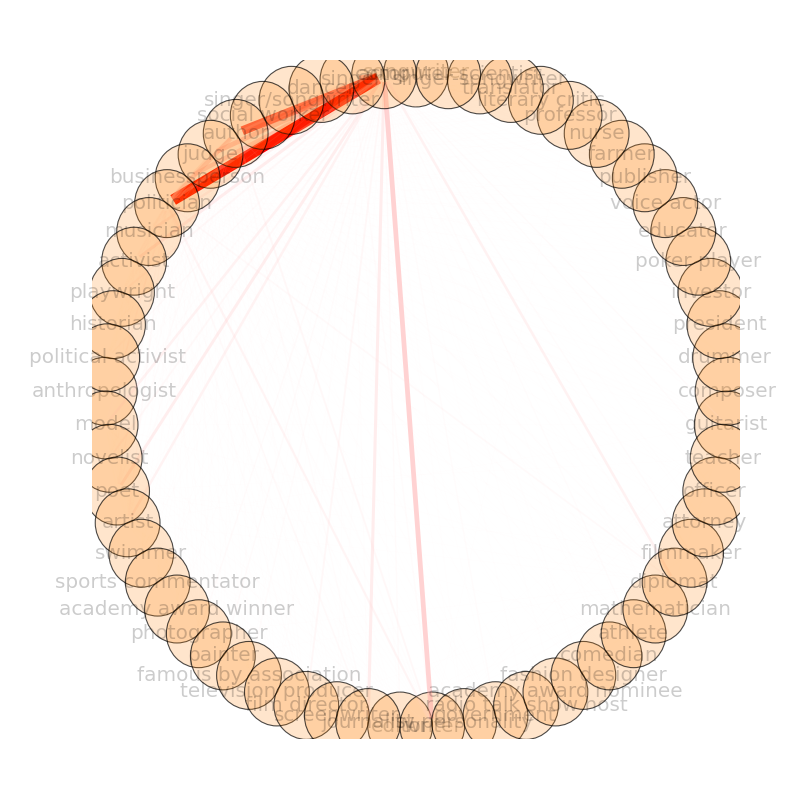

```mathematica
(* Adjust just one option stored in the graph g *)
g=SetProperty[g,EdgeStyle->ModifiedEdgePropertiesX];

Gfin=Show[g,ImagePadding->{{100,100},{100,100}}]
```